# Linear Motion

## Finding the Velocity Function

Consider a graph of Distance, s(t), vs. Time, t, for a particle moving in one direction (left-right, or up-down):

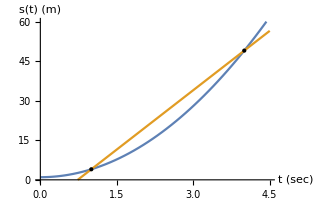

The Average Velocity over a time interval can be found by finding the slope of the secant line between the endpoints of a time interval:

V_ave=Δs/Δt=(s(t+h)-s(t))/h

From the graph of position, s(t), above, estimate the average velocity over the interval t=1 to t=3. Type your answer in the text cell:

The speedometer in your car measures instantaneous velocity, not average velocity.

Use the slider to move the secant line into a tangent line at t=1 sec:

```mathematica
(* adapted from CalcLabs Mathematica 5e pg 60 (Hollis) *)
f[x_]:=3 x^2+1;
sec[h_][x_]:=f[1]+(f[1+h]-f[1])/h(x-1);
Manipulate[
Plot[{f[x],sec[h][x]},{x,0,4.5},PlotRange->{0,60},
Epilog->Point[{{1,f[1]},{1+h,f[1+h]}}],AxesLabel->{"t (sec)","s(t) (m)"}],{{h,3},.01,3,Appearance->"Labeled"},SaveDefinitions->True]
```

Estimate the instantaneous velocity at t=1 and type your answer in this text cell:

Since the instantaneous velocity is the slope of the tangent line to the position graph, we can say that:

Velocity is the derivative of Position

v(t)=ⅆs/ⅆt  or  v(t)=s'(t)  two ways to say the same thing!

Note that you can use either the v(t)=ⅆs/ⅆt or v(t)=s'(t) notation to find the velocity function. They both say: “Find the derivative of s(t) with respect to t.”

## The Sign of Velocity

The animation below shows the motion of a red ball moving up and down. 
The black graph is the position height in meters vs. time in seconds.

Click in the following code cell (anywhere) and press [shift] [enter]. 
Then click the “play” button to see the ball’s motion up and down.

```mathematica
(* from CalcLabs Mathematica 5e pg 71 (Hollis) *)
s[t_]:=(t-2)^3-3t+9;
motion[positionf_,{t_,tmin_,tmax_},{htmin_,htmax_}]:=
Module[{track,ball,level,pt,grf,s,c,d},
s[tt_]:=positionf/.t->tt;
c=tmin-(tmax-tmin)/4;d=tmin-(tmax-tmin)/5;
track=Graphics[{Line[{{d,htmin},{d,htmax}}]}];
ball[y_]=Graphics[{PointSize[.033],Red,Point[{d,y}]}];
level[tt_,y_]=Graphics[{Line[{{d,y},{tt,y}}]}];
pt[tt_,y_]=Graphics[{PointSize[.02],Blue,Point[{tt,y}]}];
grf=Plot[s[t],{t,0,tmax},PlotStyle->Darker[Gray]];
Animate[Show[grf,track,
Plot[s[t],{t,tmin-.001,t2},PlotStyle->Thick],
Plot[Evaluate[s[t2]+s'[t2](t-t2)],{t,t2-d,t2+d},PlotStyle->Darker[Green]],level[t2,s[t2]],ball[s[t2]],
pt[t2,s[t2]],Ticks->{Range[Floor[tmin],tmax],Automatic},
AxesOrigin->Automatic,PlotRange->{{c,tmax},{htmin,htmax}},AxesLabel->{"t (sec)","s(t) (m)"}],{t2,tmin,tmax},SaveDefinitions->True,AnimationRunning->False]]
motion[s[t],{t,0,4.1},{-.5,8.5}]
```

For the interval 0≤ t≤ 4 seconds, find the following times or intervals for when:

The ball is stopped:  
The ball is moving down:  
The ball is moving up:  
The slope of the green tangent line is zero:  
The slope of the green tangent line is negative:  
The slope of the green tangent line is positive:

Since velocity is the derivative of the position function (slope of a tangent line), what is the relationship of the ball’s velocity and its direction?

Write your answer in the text cell...it should have three parts:

### When you don’t have a nice Plot to look at

Say a ball is moving along the y-axis (up and down only) with it’s position given by s(t)=t^3-6 t^2+9 t+1 meters, t≥0 seconds.

Find the interval(s) when the ball is stopped,moving up, and moving down.

To solve this, we will follow the following steps:

Find the time(s) when the ball is stopped.

Find the velocity function

Use the Power Rule to find v(t):

v(t)=ⅆs/ⅆt=3 t^2-12t+9

Set v(t)=0 and solve for t  (don’t forget units!):

0=3(t^2-4t+3)
	0=3(t-1)(t-3)
	t=1 sec, t=3 sec  (both are in our domain for t, so we keep both answers)

Create a labeled sign chart for the velocity function

Start with the blue number-line for t≥0. Notice the “wall” at t=0. 
	Mark the zeroes of v(t) with tick marks (at t=1 and t=3).
	Pick test values for each region and substitute into v(t) to find the sign.
		v(1/2)>0,  v(2)<0,  v(4)>0
	Mark the sign of v(t) (shown in red) for each region. Correct labeling is important!

Describe the interval(s) to answer the original question.

Using the sign chart:

The ball is stopped at t=1 sec and t=3 sec because v(t)=0 at these times.
The ball is moving down over (1,3) sec because v(t)<0 over this interval.
The ball is moving up over [0,1)∪(3,∞) because v(t)>0 over this interval.

Done! Working analytically is more accurate than estimating from a graph, but more error-prone when working by hand.

#### Use Mathematica to find the zeroes of velocity (instead of by hand)

Define the position function s(t)=t^3-6 t^2+9 t+1. Click in the input cell and press [shift] [enter]:

```mathematica
s[t_]=t^3-6 t^2+9 t+1
```

t^3-6 t^2+9 t+1

Find v(t): Press [shift] [enter]

```mathematica
s'[t]
```

3 t^2-12 t+9

Set s'(t)=0 and solve for t. Note the double-equal sign. The “,t” tells Mathematica to solve for t. Press [shift] [enter]:

```mathematica
Solve[s'[t]==0,t]
```

{{t→1},{t→3}}

## Acceleration

If you look at the animation of the red ball above, you will notice that the velocity changes.
Watch the animation again and see how the velocity (slope of the green line) changes with time.

Acceleration is the rate of change of velocity with respect to time...or put another way:

Acceleration is the derivative of Velocity

There are a variety of ways to write this connection with calculus:

a(t)=v'(t), a(t)=ⅆv/ⅆt, a(t)=s''(t), or a(t)=(ⅆ^2 s)/(ⅆ t^2)

Write the meaning (in English) of a(t)=v'(t) or a(t)=ⅆv/ⅆt:

Write the meaning (in English) of a(t)=s''(t) or a(t)=(ⅆ^2 s)/(ⅆ t^2):

### Velocity Increasing & Decreasing - look at acceleration

Let’s take the ball example from above and ask a new question:

Find the interval(s) when the ball’s velocity is increasing and decreasing.

Velocity will increase when v'(t)>0, (when a(t)>0) and 
velocity will decrease when v'(t)<0, (when a(t)<0).

To solve this, we will create a sign chart for acceleration following the same steps that we did for creating the velocity sign chart:

Find the acceleration function:

v(t)=ⅆs/ⅆt=3 t^2-12t+9  (from above)
	a(t)= ⅆv/ⅆt= v'(t)=6t-12   (using the Power Rule)

Set a(t)=0 and solve for t:

0=6t-12
	12=6t
	t=2 sec

Create a labeled sign chart for the acceleration function:

Start with the blue number-line for t≥0. Notice the “wall” at t=0. 
	Mark the zeroes of a(t) with tick marks (at t=2).
	Pick test values for each region and substitute into v(t) to find the sign.
		a(1)<0,  a(3)>0
	Mark the sign of a(t) (shown in green) for each region. Correct labeling is important!

And now we can answer the question:

Find the interval(s) when the ball’s velocity is increasing and decreasing.

Use Mathematica to find the zero of acceleration. Don’t forget to press [shift] [enter]:

```mathematica
Solve[s''[t]==0,t]
```

{{t→2}}

Note that this works since s(t) was already defined above and Mathematica knows what s''(t) is without calculating it directly!

## Speeding Up and Slowing Down or Speed Increasing & Speed Decreasing

Speed is the absolute value of velocity: speed=Abs[v(t)].

For example, the speedometer in a car shows speed, not velocity. When you drive in reverse, the dashboard does not show a negative value for speed!

An object is Speeding Up when v(t) and a(t) have the same sign.

If v(t) and a(t) are both positive, the object is speeding up to the right (or up).
		The velocity is positive and getting bigger. 
	If v(t) and a(t) are both negative, the object is speeding up to the left (or down).
		The velocity is negative and getting smaller (more negative).

An object is Slowing Down when v(t) and a(t) have opposite signs.

If v(t)>0 and a(t)<0, the velocity is positive and decreasing.
	If v(t)<0 and a(t)>0, the velocity is negative and increasing (getting less negative).

To find the intervals where an object is speeding up or slowing down, it is easiest to look at the sign of v(t) and a(t) together. By lining up the two sign charts and using the zeroes of both functions, we can find the intervals where v(t) and a(t) have the same or different signs:

The ball’s velocity is speeding up over (1,2)∪(3,∞) sec because v(t) and a(t) have opposite signs over these intervals.
The ball’s velocity is slowing down over [0,1)∪(2,3) sec because v(t) and a(t) have opposite signs over these intervals.

## The Derivative of Acceleration

FYI, the derivative of acceleration is called the Jerk (the 3rd derivative of position).

Do a quick Google search and find the names for the 4th, 5th, and 6th derivative of position:

4th derivative: 
5th derivative: 
6th derivative:

## Practice:

A particle moves along a line with a position function of s(t)=t^2-3t+2 for t≥0. Position is measured in feet and time in seconds.

Show that the average velocity from t=0 to t=5 is 2 feet per second:

Show that the instantaneous velocity at t=5 is 7 feet per second:

Find the intervals when the particle is moving left and right:

Find the interval(s) when the particle is speeding up.